What is used in this document:

1. Taylor expansion of variables of comparable norm: e.g. FradialForm
2. Simple Matrix Algebra: calculateHMatrix
3. Writing complex expressions in (complex) radial form: e.g.  FradialForm
4. Careful manipulations involving the arctan function: arctan
5. Making variable substitutions to simplify expressions: e.g.  calculating H21

## Function Definitions

```mathematica
(*This is an initialization cell*)
Clear["Global`*"] (*Clear Previous History*)

(*Useful Functions to use*)
absArgForm[complexExpr_,exactSolve_]:=Module[{exprArg,exprNorm},
absArgtemp1=Simplify[Re[ComplexExpand[complexExpr]]];
absArgtemp2=Simplify[Im[ComplexExpand[complexExpr]]];

exprNorm = Simplify[Sqrt[absArgtemp1^2+absArgtemp2^2]];

If[exactSolve== True,

(*Exact equations*)
absArgtemp1= FullSimplify[absArgtemp1/exprNorm];
absArgtemp2=FullSimplify[absArgtemp2/exprNorm];
absArgtemp1=Simplify[Reduce[
{Cos[exprArg]==absArgtemp1,
Sin[exprArg]==absArgtemp2,
-Pi<exprArg<Pi},exprArg]];

absArgtemp1=Solve[absArgtemp1,exprArg]; 
exprArg=exprArg/.absArgtemp1[[1]],

(*Looser Conditions*)
exprArg = ArcTan[absArgtemp2/absArgtemp1];
exprArg=exprArg+FullSimplify[ If[absArgtemp1 < 0, 
FullSimplify[If[absArgtemp2<0,-Pi,Pi]],
0] ];	

];

(*Return Expression in vector form: {Norm*Exp[I*Argument], Norm, Argument}*)
{exprNorm*Exp[I*exprArg],exprNorm,exprArg}
]

(* Will be useful for making simplications later on; taken from http://stackoverflow.com/questions/8073530/get-mathematica-to-simplify-expression-with-another-equation *)
replacementFunction[expr_,rep_,vars_]:=Module[{num=Numerator[expr],den=Denominator[expr],hed=Head[expr],base,expon},If[PolynomialQ[num,vars]&&PolynomialQ[den,vars]&&!NumberQ[den],replacementFunction[num,rep,vars]/replacementFunction[den,rep,vars],If[hed===Power&&Length[expr]==2,base=replacementFunction[expr[[1]],rep,vars];expon=replacementFunction[expr[[2]],rep,vars];PolynomialReduce[base^expon,rep,vars][[2]],If[Head[hed]===Symbol&&MemberQ[Attributes[hed],NumericFunction],Map[replacementFunction[#,rep,vars]&,expr],PolynomialReduce[expr,rep,vars][[2]]]]]]
```

## The Derivation

### Assumptions + Variable Definitions

```mathematica
(*Assumptions made throughout the document*)
$Assumptions={x>0,R>0,T>0, T<1, I0>0,ω0>0,m>0,c>0, Ω>0,T+R==1, L>0, τ>0, ξ>0, κ>0,gSQL>0, θ>0};

(*Symbolic definitions*)
s=-1;
R = 1-T;
χ=Exp[I*x];  (*x = Ωτ*) (*τ = L/c;*)
MMatrix = χ^2*{{1, 0}, {s*κC, 1}}; (*κ=8*I0*ω0/m/c^2/Ω^2;*) (*κC=4*κ/T*)
RMatrix[θ_]:=Exp[I*θ*Ω/ω0]*{ {Cos[θ], -Sin[θ]},{Sin[θ], Cos[θ]} };
Dvec=-χ/gSQL*{0,Sqrt[2*κC]}; (*gSQL = Sqrt[2*ℏ*m*Ω^2];*)

(*Simplfying assignments that will be used*)
repSimplify1=Numerator[Together[γ-T/4/τ]];
repCavityBandwith=Numerator[Together[γ-T*c/(4*L)]];
repPhi=Numerator[Together[ξ-Ω/γ]]; (*ξ = Ω/γ > 0*)
```

## No assumptions made

### Step 1: Calculate H̲ Matrix

```mathematica
(*Other equivalent but simpler approach*)
HMatrix = T*RMatrix[θ].Inverse[IdentityMatrix[2]-Sqrt[R]*MMatrix.RMatrix[2θ]].MMatrix.RMatrix[θ];
HMatrix = FullSimplify[HMatrix-Sqrt[R]*IdentityMatrix[2]];
HMatrix = FullSimplify[HMatrix];

HMatrix//MatrixForm (*Result of algebra*)
```

(((1+ⅇ^(4 ⅈ (x+θ Ω ω0))) √(1-T) T+ⅇ^(2 ⅈ (x+θ Ω ω0)) (-2+T) (T Cos[2 θ]+2 κ Sin[2 θ]))/((-1+ⅇ^(4 ⅈ (x+θ Ω ω0)) (-1+T)) T+2 ⅇ^(2 ⅈ (x+θ Ω ω0)) √(1-T) (T Cos[2 θ]+2 κ Sin[2 θ])) | (2 ⅇ^(2 ⅈ (x+θ Ω ω0)) T Sin[θ] (T Cos[θ]+2 κ Sin[θ]))/((-1+ⅇ^(4 ⅈ (x+θ Ω ω0)) (-1+T)) T+2 ⅇ^(2 ⅈ (x+θ Ω ω0)) √(1-T) (T Cos[2 θ]+2 κ Sin[2 θ]))
-(2 ⅇ^(2 ⅈ (x+θ Ω ω0)) T Cos[θ] (-2 κ Cos[θ]+T Sin[θ]))/((-1+ⅇ^(4 ⅈ (x+θ Ω ω0)) (-1+T)) T+2 ⅇ^(2 ⅈ (x+θ Ω ω0)) √(1-T) (T Cos[2 θ]+2 κ Sin[2 θ])) | ((1+ⅇ^(4 ⅈ (x+θ Ω ω0))) √(1-T) T+ⅇ^(2 ⅈ (x+θ Ω ω0)) (-2+T) (T Cos[2 θ]+2 κ Sin[2 θ]))/((-1+ⅇ^(4 ⅈ (x+θ Ω ω0)) (-1+T)) T+2 ⅇ^(2 ⅈ (x+θ Ω ω0)) √(1-T) (T Cos[2 θ]+2 κ Sin[2 θ])))

### Step2: Calculate F⃗

```mathematica
Fvec=Sqrt[T]*Inverse[IdentityMatrix[2]-MMatrix*RMatrix[2*θ]*Sqrt[R]].Dvec;
Fvec=Simplify[Fvec];

Fvec //MatrixForm
```

(0
(2 √2 ⅇ^(ⅈ x) √κ)/(-gSQL+ⅇ^(2 ⅈ (x+θ Ω ω0)) gSQL √(1-T) Cos[2 θ]))

## Assumption 1: Ω<< ω_0

### Step 1: Calculate H̲ Matrix

```mathematica
RMatrix[θ_]:={ {Cos[θ], -Sin[θ]},{Sin[θ], Cos[θ]} };
(*Other equivalent but simpler approach*)
HMatrix = T*RMatrix[θ].Inverse[IdentityMatrix[2]-Sqrt[R]*MMatrix.RMatrix[2θ]].MMatrix.RMatrix[θ];
HMatrix = FullSimplify[HMatrix-Sqrt[R]*IdentityMatrix[2]];
HMatrix = FullSimplify[HMatrix];

HMatrix//MatrixForm (*Result of algebra*)
```

(((1+ⅇ^(4 ⅈ x)) √(1-T)+ⅇ^(2 ⅈ x) (-2+T) (Cos[2 θ]+κC Cos[θ] Sin[θ]))/(-1+ⅇ^(4 ⅈ x) (-1+T)+ⅇ^(2 ⅈ x) √(1-T) (2 Cos[2 θ]+κC Sin[2 θ])) | (ⅇ^(2 ⅈ x) T Sin[θ] (2 Cos[θ]+κC Sin[θ]))/(-1+ⅇ^(4 ⅈ x) (-1+T)+ⅇ^(2 ⅈ x) √(1-T) (2 Cos[2 θ]+κC Sin[2 θ]))
(ⅇ^(2 ⅈ x) T Cos[θ] (κC Cos[θ]-2 Sin[θ]))/(-1+ⅇ^(4 ⅈ x) (-1+T)+ⅇ^(2 ⅈ x) √(1-T) (2 Cos[2 θ]+κC Sin[2 θ])) | ((1+ⅇ^(4 ⅈ x)) √(1-T)+ⅇ^(2 ⅈ x) (-2+T) (Cos[2 θ]+κC Cos[θ] Sin[θ]))/(-1+ⅇ^(4 ⅈ x) (-1+T)+ⅇ^(2 ⅈ x) √(1-T) (2 Cos[2 θ]+κC Sin[2 θ])))

```mathematica
RMatrix[θ_]:={ {Cos[θ], -Sin[θ]},{Sin[θ], Cos[θ]} };
(*Other equivalent but simpler approach*)
HMatrix = T*Inverse[IdentityMatrix[2]-Sqrt[R]*RMatrix[θ].MMatrix.RMatrix[θ]].RMatrix[θ].MMatrix.RMatrix[θ];
HMatrix = FullSimplify[HMatrix-Sqrt[R]*IdentityMatrix[2]];
HMatrix = FullSimplify[HMatrix];

HMatrix//MatrixForm (*Result of algebra*)
```

(((1+ⅇ^(4 ⅈ x)) √(1-T)+ⅇ^(2 ⅈ x) (-2+T) (Cos[2 θ]+κC Cos[θ] Sin[θ]))/(-1+ⅇ^(4 ⅈ x) (-1+T)+ⅇ^(2 ⅈ x) √(1-T) (2 Cos[2 θ]+κC Sin[2 θ])) | (ⅇ^(2 ⅈ x) T Sin[θ] (2 Cos[θ]+κC Sin[θ]))/(-1+ⅇ^(4 ⅈ x) (-1+T)+ⅇ^(2 ⅈ x) √(1-T) (2 Cos[2 θ]+κC Sin[2 θ]))
(ⅇ^(2 ⅈ x) T Cos[θ] (κC Cos[θ]-2 Sin[θ]))/(-1+ⅇ^(4 ⅈ x) (-1+T)+ⅇ^(2 ⅈ x) √(1-T) (2 Cos[2 θ]+κC Sin[2 θ])) | ((1+ⅇ^(4 ⅈ x)) √(1-T)+ⅇ^(2 ⅈ x) (-2+T) (Cos[2 θ]+κC Cos[θ] Sin[θ]))/(-1+ⅇ^(4 ⅈ x) (-1+T)+ⅇ^(2 ⅈ x) √(1-T) (2 Cos[2 θ]+κC Sin[2 θ])))

#### Observations

We have that H11=H22

```mathematica
HMatrix[[1,1]]-HMatrix[[2,2]]
```

0

All of H’s entries share the same denominator:

```mathematica
HMatDenominator = (-1+ⅇ^(4 ⅈ x) (-1+T)) T+2 ⅇ^(2 ⅈ x) √(1-T) (T Cos[2 θ]+2 κ Sin[2 θ]);
HMatrix*HMatDenominator//MatrixForm
```

(ⅇ^(2 ⅈ x) (2 √(1-T) T Cos[2 x]+(-2+T) (T Cos[2 θ]+2 κ Sin[2 θ])) | 2 ⅇ^(2 ⅈ x) T Sin[θ] (T Cos[θ]+2 κ Sin[θ])
-2 ⅇ^(2 ⅈ x) T Cos[θ] (-2 κ Cos[θ]+T Sin[θ]) | ⅇ^(2 ⅈ x) (2 √(1-T) T Cos[2 x]+(-2+T) (T Cos[2 θ]+2 κ Sin[2 θ])))

### Step2: Calculate F⃗

```mathematica
Fvec=Sqrt[T]*Inverse[IdentityMatrix[2]-MMatrix*RMatrix[2*θ]*Sqrt[R]].Dvec;
Fvec=Simplify[Fvec];

Fvec //MatrixForm
```

(0
(2 √2 ⅇ^(ⅈ x) √κ)/(-gSQL+ⅇ^(2 ⅈ x) gSQL √(1-T) Cos[2 θ]))

## Full Set of Assumptions

### Step 2: Make approximations (because T and x are of comparable small norm) to simplify the H̲ Matrix

#### First try to simplify the denominator of the HMatrix

```mathematica
HMatDenominatorSeries = Series[HMatDenominator/.{x-> x*ϵ,T-> T*ϵ,θ-> θ*ϵ,κ-> κ*ϵ},{ϵ,0,2}];
HMatDenominatorSeries = FullSimplify[Normal[HMatDenominatorSeries]/.{ϵ-> 1}]
```

8 θ κ

```mathematica
HMatrix12=Series[(HMatrix)/.{x-> x*ϵ,T-> T*ϵ,θ-> θ*ϵ,κC-> κC*ϵ},{ϵ,0,0}];
HMatrix12 = Simplify[Normal[HMatrix12]];
HMatrix12 = Simplify[HMatrix12/.{ϵ-> 1}]

(*Subscript[H, 11] in  radial form*)
```

{{(T^2+8 (2 x^2+θ (-2 θ+κC)))/(T^2-8 ⅈ T x-8 (2 x^2+θ (-2 θ+κC))),-(8 T θ)/(T^2-8 ⅈ T x-8 (2 x^2+θ (-2 θ+κC)))},{(T (8 θ-4 κC))/(T^2-8 ⅈ T x-8 (2 x^2+θ (-2 θ+κC))),(T^2+8 (2 x^2+θ (-2 θ+κC)))/(T^2-8 ⅈ T x-8 (2 x^2+θ (-2 θ+κC)))}}

```mathematica
HMatrix12=Series[(HMatrix[[2,1]]*HMatDenominator)/.{x-> x*ϵ,T-> T*ϵ,θ-> θ*ϵ,κ-> κ*ϵ},{ϵ,0,3}];
HMatrix12 = Simplify[Normal[HMatrix12]];
HMatrix12 = Simplify[HMatrix12/.{ϵ-> 1}]

(*Subscript[H, 11] in  radial form*)
```

2 T (-T θ+2 κ+4 ⅈ x κ)

```mathematica
|
```

```mathematica
Expand[(16 (2+T) θ+(T (T-4 ⅈ x)^2)/κ)(16 (2+T) θ+(T (T-4 ⅈ x)^2)/κ)]
```

1024 θ^2+1024 T θ^2+256 T^2 θ^2+T^6/κ^2-(16 ⅈ T^5 x)/κ^2-(96 T^4 x^2)/κ^2+(256 ⅈ T^3 x^3)/κ^2+(256 T^2 x^4)/κ^2+(64 T^3 θ)/κ+(32 T^4 θ)/κ-(512 ⅈ T^2 x θ)/κ-(256 ⅈ T^3 x θ)/κ-(1024 T x^2 θ)/κ-(512 T^2 x^2 θ)/κ

```mathematica
HMatrix12=Series[(HMatrix[[1,2]])/.{x-> x*ϵ,T-> T*ϵ,θ-> θ*ϵ,κ-> κ*ϵ},{ϵ,0,2}];
HMatrix12 = Simplify[Normal[HMatrix12]];
HMatrix12 = Simplify[HMatrix12/.{ϵ-> 1}]

HMatrix12 = Simplify[HMatrix12/.{x-> Ω*τ}];
HMatrix12 = Simplify[HMatrix12/.{κ-> T*τ*ι/4/Ω^2}];
HMatrix12 = FullSimplify[HMatrix12/.{θ->Δ*τ}]
HMatrix12=Simplify[replacementFunction[HMatrix12,repSimplify1,{γ, T, τ}]]
HMatrix12 = FullSimplify[HMatrix12/.{T->γ*4*τ}]



(*Subscript[H, 11] in  radial form*)
```

(T (T^4-8 ⅈ T^3 x+32 T θ κ+64 θ^2 κ^2-16 T^2 (x^2-θ (θ+κ))))/(128 θ κ^2)

(T (4 (2+T) Δ ι τ^2 Ω^2+Ω^4 (T-4 ⅈ τ Ω)^2+4 Δ^2 (ι^2 τ^4+4 τ^2 Ω^4)))/(8 Δ ι^2 τ^3)

(T (4 (2+T) Δ ι τ^2 Ω^2+Ω^4 (T-4 ⅈ τ Ω)^2+4 Δ^2 (ι^2 τ^4+4 τ^2 Ω^4)))/(8 Δ ι^2 τ^3)

(2 γ (2 Δ ι (1+2 γ τ) Ω^2+4 (γ-ⅈ Ω)^2 Ω^4+Δ^2 (ι^2 τ^2+4 Ω^4)))/(Δ ι^2)

```mathematica
testExpr=Expand[(T^4-8 ⅈ T^3 x+32 T θ κ+64 θ^2 κ^2-16 T^2 (x^2-θ (θ+κ)))*(T^4+8 ⅈ T^3 x+32 T θ κ+64 θ^2 κ^2-16 T^2 (x^2-θ (θ+κ)))]
FullSimplify[testExpr]
```

T^8+32 T^6 x^2+256 T^4 x^4+32 T^6 θ^2-512 T^4 x^2 θ^2+256 T^4 θ^4+64 T^5 θ κ+32 T^6 θ κ-1024 T^3 x^2 θ κ-512 T^4 x^2 θ κ+1024 T^3 θ^3 κ+512 T^4 θ^3 κ+1024 T^2 θ^2 κ^2+1024 T^3 θ^2 κ^2+384 T^4 θ^2 κ^2-2048 T^2 x^2 θ^2 κ^2+2048 T^2 θ^4 κ^2+4096 T θ^3 κ^3+2048 T^2 θ^3 κ^3+4096 θ^4 κ^4

T^4 (T^4+256 (x^2-θ^2)^2+32 T^2 (x^2+θ^2))+32 T^3 (2+T) θ (T^2+16 (-x^2+θ^2)) κ+128 T^2 θ^2 (8+T (8+3 T)-16 x^2+16 θ^2) κ^2+2048 T (2+T) θ^3 κ^3+4096 θ^4 κ^4

```mathematica
HMatrix[[1,2]]
```

(2 ⅇ^(2 ⅈ x) T Sin[θ] (T Cos[θ]+2 κ Sin[θ]))/((-1+ⅇ^(4 ⅈ x) (-1+T)) T+2 ⅇ^(2 ⅈ x) √(1-T) (T Cos[2 θ]+2 κ Sin[2 θ]))

```mathematica
HMatrix12=Series[(HMatrix[[1,2]]),{θ,0,1}];
HMatrix12=Series[(HMatrix12)/.{x-> x*ϵ,T-> T*ϵ,κ-> κ*ϵ},{ϵ,0,0}];

HMatrix12 = Simplify[Normal[HMatrix12]];
HMatrix12 = Simplify[HMatrix12/.{ϵ-> 1}]
```

(4 T (T^2+T (-2+4 ⅈ x)+8 ⅈ x) θ)/(T-4 ⅈ x)^3

#### Try to simplify the argument by using a different strategy: try to reduce the number of variables to 1

```mathematica
HMatrix11=FullSimplify[HMatrix11];
HMatrix11=Simplify[replacementFunction[HMatrix11,repSimplify1,{x, T}]] ;(*Replace T/4x by φ*)

(*Now that the we have reduced the expression to one parameter (that is positive and so does not have any weird conditions on it), try to write it in abs arg form again*)
Simplify[ Assuming[ φ>0,(absArgForm[HMatrix11,False])[[3]] ] ]
```

π-ArcTan[T^3/(T^3 φ+16 θ κ φ+2 T^2 θ κ φ)]

#### Use ArcTan Identities to simplify the above expression

From (http://en.wikipedia.org/wiki/Inverse_trigonometric_functions#Arctangent_addition_formula), we have that

2tan^-1(u)=tan^-1((2u)/(1-u^2))[Mod π]

The Mod π is because tan^-1 is defined over the domain [-π/2, π/2]. Hence,

ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])=-ArcTan[(2 φ)/(1-φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])
=-2ArcTan[φ]+(Piecewise[{{π, φ<1}, {0, True}}])+Mod[π]

When is |-2 tan^-1 u|>π/2? First, we note that φ>0 so that | -2 tan^-1 φ |=| 2 tan^-1 φ |=2 tan^-1 φ  (because the inverse tangent of a positive number is positive). We ask when is tan^-1 φ>π/4?

```mathematica
Simplify[Reduce[ArcTan[φ]> π/4,φ]]
```

φ>1

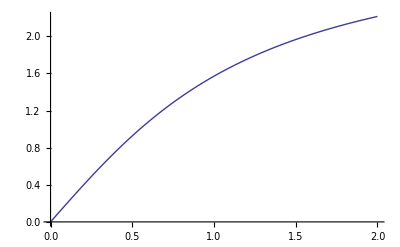

```mathematica
(*Visual representation for verification purposes*)
Plot[{2*ArcTan[φ]},{φ,0,2},
AxesLabel-> {φ}]
```

Hence, when φ>1, -2ArcTan[φ]<-π/2 and so we have to add π to remedy the issue: we obtain that ArcTan[(2 φ)/(-1+φ^2)]=-2ArcTan[φ]+(Piecewise[{{0, φ<1}, {π, φ>1}}])
⟹ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])=-2ArcTan[φ]+(Piecewise[{{0, φ<1}, {π, φ>1}}])+(Piecewise[{{π, φ<1}, {0, True}}])
=-2ArcTan[φ]+π

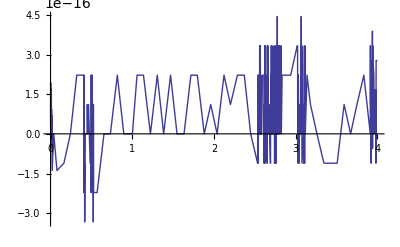

```mathematica
(*Visual representation for verification purposes*)
Plot[(ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])-(π-2*ArcTan[φ])),{φ,0,4},
AxesLabel-> {φ}]
```

Finally,we use the identity that arctan(1/x)=-π/2-arctan(x) to obtain that:


H_11=ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{π, T<4 x}, {0, True}}])))
=ArcTan[(2 φ)/(-1+φ^2)]+(Piecewise[{{π, φ<1}, {0, True}}])
=-2ArcTan[φ]+π
=2(π/2-ArcTan[φ])=2ArcTan[1/φ]
=2ArcTan[(4x)/T]
⇒H_11=H_22=exp(2ⅈArcTan[(4x)/T])
=e^(2ⅈϕ), 
where ϕ≡ArcTan[(4x)/T]

```mathematica
(*Side Note: This could have also worked*)

Series[HMatrix[[1,1]]/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,0}];

Simplify[Normal[%]];
Simplify[%/.{x-> Ω*(L/c)}];
Simplify[replacementFunction[%,repCavityBandwith,{c, T, L}]];
temp = Simplify[replacementFunction[%,repPhi,{Ω, γ}]];

HMatrix11absArgForm = (absArgForm[temp,True])[[1]]
```

ⅇ^(2 ⅈ ArcTan[ξ])

#### Simplify the off-diagonal term by making use of approximations: H_21

```mathematica
HMatrix21= HMatrix[[2,1]];

(*Find the lowest order term*)
Manipulate[Normal[Series[HMatrix21/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,o}]],{o,-10,10,1}]
```

```mathematica
(*-1 is our winner*)
HMatrix21 = Series[HMatrix[[2,1]]/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,-1}];
HMatrix21 = Simplify[Normal[HMatrix21]];
HMatrix21 = Simplify[HMatrix21/.{ϵ-> 1}];

(*Try the radial form to see if it is simple*)
Simplify[(absArgForm[HMatrix21,False])[[1]]]
```

(4 ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{-π, T>4 x}, {0, True}}]))) T κ)/(T^2+16 x^2)

The argument of the above expression can be written

ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{-π, T>4 x}, {0, True}}])))=ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{π, T>4 x}, {0, True}}])))
=-ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{2π, T>4 x}, {π, True}}])))
=-ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{0, T>4 x}, {π, True}}])))
=-ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{0, T>4 x}, {π, T<4x}}])))
=-ⅇ^(ⅈ (ArcTan[(8 T x)/(T^2-16 x^2)]+(Piecewise[{{π, T<4 x}, {0, True}}])))
=-H_11=exp(2ⅈArcTan[(4x)/T])
The last equality comes from using result H11

⟹H_21~T_0(H_11)(-(4  T κ)/(T^2+16 x^2))
where T_0(H_11) is the Taylor expansion of H_11 up to zeroth order.

Now we work on rewriting -(4  T κ)/(T^2+16 x^2) in terms of physical variables:

-(4  T κ)/(T^2+16 x^2)=-(4  T κ)/(T^2+16 x^2)
=-T/(T^2+16 x^2)4(8 I_0 ω_0)/(mc^2 Ω^2)=-T/(T^2+16 x^2)TL/cΩ^2(8(4I_0/T)ω_0)/mLc
=-T/(Ω^2(T^2+16 Ω^2 τ^2))Tτ(8 I_c ω_0)/mLc=-(T^2 τι_c)/(Ω^2(T^2+16 Ω^2 τ^2))
=-(T^2 τι_c)/(16 τ^2 Ω^2((T/4τ)^2+Ω^2))=-(T(T/4τ)ι_c)/(4Ω^2((T/4τ)^2+Ω^2))
=-(T×γ×ι_c)/(4Ω^2(γ^2+Ω^2))=-T/8(2γ×ι_c)/(Ω^2(γ^2+Ω^2))

Hence, using result H11
H_21=-e^(2ⅈϕ)(4  T κ)/(T^2+16 x^2)
=-e^(2ⅈϕ)T/8(2γ×ι_c)/(Ω^2(γ^2+Ω^2))

#### Simplify the off-diagonal term by making use of approximations (the better way): H_21

Use the observations exact observations that H_21∝H_11 and the constant of proportionality is real

```mathematica
H21DivH11= HMatrix[[2,1]]/HMatrix[[1,1]];

H21DivH11 = Series[H21DivH11/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,-1}];
H21DivH11 = FullSimplify[Normal[H21DivH11]];
H21DivH11 = FullSimplify[H21DivH11/.{ϵ-> 1}];

H21DivH11=Simplify[H21DivH11/.{κ-> 8*I0*ω0/m/c^2/Ω^2,x-> Ω*L/c}];

H21DivH11=Simplify[replacementFunction[H21DivH11,repCavityBandwith,{c, T, L}]]

varChangeω0=ω0/.(Solve[ι==8*ω0*(4*I0/T)/(L*c*m),ω0])[[1]];
H21DivH11=Simplify[H21DivH11/.{ω0-> varChangeω0}]

H21DivH11=Simplify[replacementFunction[H21DivH11,repCavityBandwith,{c, T, L}]]
```

-(2 I0 T ω0)/(L^2 m Ω^2 (γ^2+Ω^2))

-(c T^2 ι)/(16 L Ω^2 (γ^2+Ω^2))

-(T γ ι)/(4 Ω^2 (γ^2+Ω^2))

Hence, we obtain (using result H11) that H_21/H_11=-T/8(2 γ ι)/(Ω^2 (γ^2+Ω^2))+O(0)
⟹H_21=-e^(2ⅈϕ)T/8(2 γ ι)/(Ω^2 (γ^2+Ω^2))+O(0)
which is the same as result1 H22.

### Step3: Calculate F⃗

```mathematica
Fvec=Sqrt[T]*Inverse[IdentityMatrix[2]-MMatrix*RMatrix[2*θ]*Sqrt[R]].Dvec;
Fvec=Simplify[Fvec];

Fvec //MatrixForm
```

(0
(2 √2 ⅇ^(ⅈ x) √κ)/(-gSQL+ⅇ^(2 ⅈ (x+θ Ω ω0)) gSQL √(1-T) Cos[2 θ]))

#### Observations on calculated F⃗ matrix

```mathematica
Simplify[Im[ComplexExpand[Fvec[[2]]]]]
```

(√2 (1+√(1-T)) √κ Sin[x])/(gSQL (-2+T+2 √(1-T) Cos[2 x]))

Observations:
 F⃗ is definitely not real valued. 
 F⃗ is of the form(0
F_2)

### Step4: Use that T and x are of small comparable norm to make simplifications

#### Try to write F⃗ in radial form

```mathematica
Fvec2= Fvec[[2]];

(*Find the lowest order term*)
Manipulate[Normal[Series[Fvec2/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,o}]],{o,-10,10,1}]
```

```mathematica
(*-1 is our winner*)
Fvec2= Fvec[[2]];

Fvec2 = Series[Fvec2/.{x-> x*ϵ,T-> T*ϵ},{ϵ,0,-1}];
Fvec2 = Simplify[Normal[Fvec2]];
Fvec2 = Simplify[Fvec2/.{ϵ-> 1}];

(absArgForm[Fvec2,False])[[1]]
```

(2 √2 ⅇ^(ⅈ (-π+ArcTan[(4 x)/T])) √(κ/(T^2+16 x^2)))/gSQL

We remember the definition  ϕ≡ArcTan[(4x)/T] (result1 H22). Further, 
-g_SQL×F_2=2 √2 ⅇ^ⅈϕ √(κ/(T^2+16 x^2))
=2 √2 ⅇ^ⅈϕ √(1/(4T)(4Tκ)/(T^2+16 x^2))
=2 √2 ⅇ^ⅈϕ √(1/(4T)T/8(2γ×ι_c)/(Ω^2(γ^2+Ω^2)))
= ⅇ^ⅈϕ 1/2 √((2γ×ι_c)/(Ω^2(γ^2+Ω^2)))
where we used result1 H22 in the third equality.

Hence, F_2=-ⅇ^ⅈϕ 1/(2 g_SQL)√((2γ×ι_c)/(Ω^2(γ^2+Ω^2))). Using observations Fvector, we can now write that F⃗=-(0
ⅇ^ⅈϕ 1/(2 g_SQL)√((2γ×ι_c)/(Ω^2(γ^2+Ω^2)))).